```mathematica
SetDirectory[NotebookDirectory[]];
```

# Pre

```mathematica
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,1000,5000}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ300=75.8;
ν300=-482.^2;
c300=1.7*10^-3*(10^3)^3;
M=300.;
```

# Mean-field two-point function

## threshold functions

```mathematica
F1[q_,ρ_,h_,T_,μ_]:=q/(2 √(q^2+mf2[h,ρ]))(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]);
F1F1m[q_,p0_,ps_,x_,ρ_,h_,T_,μ_]:=q^3/(4 √(q^2+mf2[h,ρ])√((q^2+ps^2-2q ps x)+mf2[h,ρ]))((-0.+nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]+nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ]-nfa[mf2[h,ρ],q,T,μ])/(ⅈ p0-√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(nff[mf2[h,ρ],q,T,μ]-nff[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])-√((q^2+ps^2-2q ps x)+mf2[h,ρ]))+(0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],√(q^2+ps^2-2q ps x),T,μ])/(ⅈ p0+√(q^2+mf2[h,ρ])+√((q^2+ps^2-2q ps x)+mf2[h,ρ])));
```

## thermal equation

```mathematica
gamma2thr[p0_,ps_,ρ_,h_,T_,μ_]:=-(2π h^2 Nc)/(2π)^3 NIntegrate[q^2/q((*2F1[q,ρ,h,T,μ]*)-(p0^2+ps^2)/q^2 F1F1m[q,p0,ps,x,ρ,h,T,μ]),{q,0.,10.,20.,30.,40.,50.,60.,70.,80.,90.,100.,200.,300.,400.,500.,5000.},{x,-1,1},
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)}];
```

## Regularized vacuum

```mathematica
gammavac0[p0_,ps_,ρ_,h_,Mmass_,MZ_]:=-(Nc h^2)/(8 π^2)((2Log[(√mf2[h,ρ])/Mmass])mf2[h,ρ]+(p0^2+ps^2)/2 NIntegrate[Log[(-(p0^2+ps^2)(x-1)^2-x(p0^2+ps^2)+(p0^2+ps^2)+mf2[h,ρ])/MZ^2],{x,0,1}])-(Nc h^2 mf2[h,ρ])/(16 π^2)+(p0^2+ps^2)+(λ300 ρ+ν300);
```

## full two-point function

```mathematica
gamma2[p0_,ps_,ρ_,h_,T_,μ_,Mmass_,MZ_]:=(*gamma2thr[p0,ps,ρ,h,T,μ]+*)gammavac0[p0,ps,ρ,h,Mmass,MZ];
```

# Plot data

```mathematica
fpi=Flatten[Transpose[Import["./renormal/M300.dat"]]];
fpimu0=fpi[[1;;300]];
fpimu100=fpi[[301;;600]];
fpimu200=fpi[[601;;900]];
fpimu250=fpi[[901;;1200]];
fpimu290=fpi[[1201;;1500]];
fpimu300=fpi[[1501;;1800]];
```

```mathematica
a=ParallelTable[gamma2[-ⅈ(ω+ⅈ*0.1),10.,92.32^2/2,6.5,1.,0.,300.,300.],{ω,1,700,2}];
```

```mathematica
(*a=Flatten[specmu0T100,1];*)
```

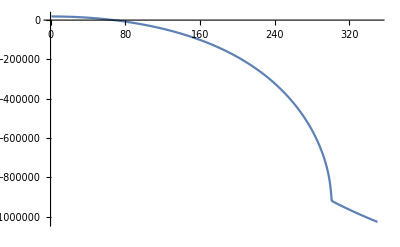

```mathematica
ListLinePlot[Re[a]]
```

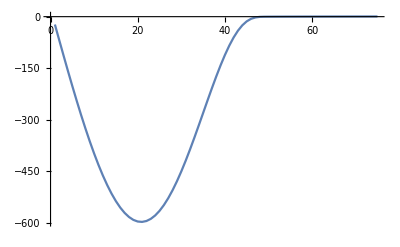

```mathematica
ListLinePlot[Im[a],PlotRange->All]
```

```mathematica
Export["./specmu250T100.dat",a]
```

./specmu250T100.dat